```mathematica
q=1
kB=1
NA=1
ND=1
epsir=1
epsi0=1
T=1
VD=1
XD=Function[{Vi},Sqrt[(2 epsir epsi0 (NA+ND)(VD-Vi))/(q NA ND)]]
xp=Function[{Vi},-XD[Vi]/2]
xn=Function[{Vi},+XD[Vi]/2]
Lp=1
pp0=NA
nn0=ND
V=Function[{x,Vi},
Piecewise[{
{0,x<=xp[Vi]},
{+((q NA)/(2epsir epsi0))x^2-((q NA xp[Vi])/(epsir epsi0))x+(q NA xp[Vi]^2)/(2 epsir epsi0),xp[Vi]<x<0},
{-((q ND)/(2epsir epsi0))x^2+((q ND xn[Vi])/(epsir epsi0))x-(q ND xn[Vi]^2)/(2 epsir epsi0)+VD-Vi,xn[Vi]>x>=0},
{VD-Vi,x>=xn[Vi]}
}]
]
Manipulate[{xn[Vi],xp[Vi]},{{Vi,0},-0.5,0.5}]
Manipulate[
Plot[V[x,Vi],{x,2xp[0],2xn[0]},
Frame->True,
GridLines->Automatic,
PlotPoints->2000
],{{Vi,0},-0.5,0.5}]
px=Function[{x,Vi},
Piecewise[{
{pp0 Exp[(-q V[x,Vi])/(kB T)],x<=xn[Vi]},
{pp0 Exp[(-q VD)/(kB T)]+pp0 Exp[-(q VD)/(kB T)](Exp[(q Vi)/(kB T)]-1)Exp[(xn[Vi]-x)/Lp],x>xn[Vi]}
}]
]
nx=Function[{x,Vi},
Piecewise[{
{nn0 Exp[(q V[x,Vi]-q (VD-Vi))/(kB T)],x>=xp[Vi]},
{nn0 Exp[(-q VD)/(kB T)]+nn0 Exp[-(q VD)/(kB T)](Exp[(q Vi)/(kB T)]-1)Exp[(x-xp[Vi])/Lp],x<xp[Vi]}
}]
]
Manipulate[
Plot[{px[x,Vi],nx[x,Vi]},{x,4xp[0],4xn[0]},
PlotRange->{0,1.2},
Frame->True,
GridLines->Automatic,
PlotPoints->2000
],{{Vi,0},-1,1}]
Simplify[px[x,0]]
Simplify[px[x,+0.5]]
Simplify[px[x,-0.5]]
Simplify[nx[x,0]]
Simplify[nx[x,+0.5]]
Simplify[nx[x,-0.5]]
Simplify[V[x,0]]
Simplify[V[x,+0.5]]
Simplify[V[x,-0.5]]
```

1

1

1

«5 more identical outputs»

Function[{Vi},√((2 epsir epsi0 (NA+ND) (VD-Vi))/(q NA ND))]

Function[{Vi},-XD[Vi]/2]

Function[{Vi},1/2 (+XD[Vi])]

1

1

1

Function[{x,Vi},Piecewise[{{0, x≤xp[Vi]}, {+(q NA)/(2 epsir epsi0) x^2-((q NA xp[Vi]) x)/(epsir epsi0)+(q NA xp[Vi]^2)/(2 epsir epsi0), xp[Vi]<x<0}, {-((q ND) x^2)/(2 epsir epsi0)+((q ND xn[Vi]) x)/(epsir epsi0)-(q ND xn[Vi]^2)/(2 epsir epsi0)+VD-Vi, xn[Vi]>x≥0}, {VD-Vi, x≥xn[Vi]}}]]

Function[{x,Vi},Piecewise[{{pp0 Exp[-(q V[x,Vi])/(kB T)], x≤xn[Vi]}, {pp0 Exp[-(q VD)/(kB T)]+pp0 Exp[-(q VD)/(kB T)] (Exp[(q Vi)/(kB T)]-1) Exp[(xn[Vi]-x)/Lp], x>xn[Vi]}}]]

Function[{x,Vi},Piecewise[{{nn0 Exp[(q V[x,Vi]-q (VD-Vi))/(kB T)], x≥xp[Vi]}, {nn0 Exp[-(q VD)/(kB T)]+nn0 Exp[-(q VD)/(kB T)] (Exp[(q Vi)/(kB T)]-1) Exp[(x-xp[Vi])/Lp], x<xp[Vi]}}]]

Piecewise[{{1, x≤-1}, {1/ⅇ, x≥1}, {ⅇ^(-1/2 (1+x)^2), -1<x<0}, {ⅇ^(1/2 (-1-2 x+x^2)), True}}]

Piecewise[{{0.778801 ⅇ^(0.5 (-1.41421+x) x), 0≤x≤0.707107}, {1, x≤-0.707107}, {0.778801 ⅇ^(-0.5 x (1.41421+x)), -0.707107<x<0}, {1/ⅇ+0.484012 ⅇ^-x, True}}]

Piecewise[{{0.472367 ⅇ^(0.5 (-2.44949+x) x), 0≤x≤1.22474}, {1, x≤-1.22474}, {0.472367 ⅇ^(-0.5 x (2.44949+x)), -1.22474<x<0}, {1/ⅇ-0.492625 ⅇ^-x, True}}]

Piecewise[{{1, x≥1}, {1/ⅇ, x≤-1}, {ⅇ^(-1/2 (-1+x)^2), 0≤x<1}, {ⅇ^(-1/2+x+x^2/2), True}}]

Piecewise[{{0.778801 ⅇ^(0.5 x (1.41421+x)), -0.707107≤x<0}, {1., x≥0.707107}, {0.778801 ⅇ^(-0.5 (-1.41421+x) x), 0≤x<0.707107}, {0.367879+0.484012 ⅇ^x, True}}]

Piecewise[{{0.472367 ⅇ^(0.5 x (2.44949+x)), -1.22474≤x<0}, {1., x≥1.22474}, {0.472367 ⅇ^(-0.5 (-2.44949+x) x), 0≤x<1.22474}, {0.367879-0.492625 ⅇ^x, True}}]

Piecewise[{{1, x≥1}, {1/2+x-x^2/2, 0≤x<1}, {1/2 (1+x)^2, -1<x<0}, {0, True}}]

Piecewise[{{0.5, x≥0.707107}, {0.25+0.707107 x-0.5 x^2, 0≤x<0.707107}, {0.5 (0.5+1.41421 x+x^2), -0.707107<x<0}, {0, True}}]

Piecewise[{{1.5, x≥1.22474}, {0.75+1.22474 x-0.5 x^2, 0≤x<1.22474}, {0.5 (1.5+2.44949 x+x^2), -1.22474<x<0}, {0, True}}]

LessEqual::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

LessEqual::nord: 尝试使用 0.-0.447214 ⅈ 进行无效的比较.

Less::nord: 尝试使用 0.-0.447214 ⅈ 进行无效的比较.

General::stop: 在本次计算中，Less::nord 的进一步输出将被抑制.

Greater::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

GreaterEqual::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

Greater::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

LessEqual::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

General::stop: 在本次计算中，LessEqual::nord 的进一步输出将被抑制.

Greater::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

General::stop: 在本次计算中，Greater::nord 的进一步输出将被抑制.

GreaterEqual::nord: 尝试使用 0.+0.447214 ⅈ 进行无效的比较.

General::stop: 在本次计算中，GreaterEqual::nord 的进一步输出将被抑制.

```mathematica
N[px[1,0]]
px[0.7071067811865477,+0.5]
px[1.2247448713915887,-0.5]
N[px[0,0]]
px[0,+0.5]
px[0,-0.5]
```

0.367879

0.606531

0.22313

0.606531

0.778801

0.472367

Function[{x,A,B,xA,xB},Piecewise[{{-((x-xA)^2 (-(B-A)))/(2 xA^2)+A, x<0}, {(+(x-xB)^2 (-(B-A)))/(2 xB^2)+B, x≥0}}]]

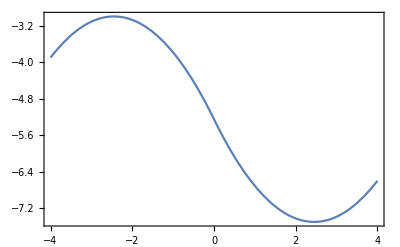

Piecewise[{{-3-0.375027 (2.4494+x)^2, x<0}, {-7.5+0.375027 (-2.4494+x)^2, x≥0}, {0, True}}]

```mathematica
FV=Function[{x,A,B,xA,xB},
Piecewise[{
{-(x-xA)^2(-(B-A)/(2 xA^2))+A,x<0},
{+(x-xB)^2(-(B-A)/(2 xB^2))+B,x>=0}
}]
]
Plot[FV[x,-3,-7.5,-2*1.2247,+2*1.2247],{x,-4,4},Frame->True,PlotRange->All]
FV[x,-3,-7.5,-2*1.2247,+2*1.2247]
```